# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

## Setup

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2.3.20,BA.2.75,BA.2.75.2,BA.2.75.3,BA.4,BA.4.1,BA.4.6,BA.4.6.5,BA.5,BA.5.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.22,BA.5.1.23,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.23,BA.5.2.28,BA.5.2.31,BA.5.2.34,BA.5.2.35,BA.5.2.6,BA.5.2.9,BA.5.5,BA.5.5.1,BA.5.6,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.1.2.1,BE.1.4,BE.3,BF.10,BF.11,BF.13,BF.14,BF.21,BF.24,BF.25,BF.26,BF.27,BF.32,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.8,BK.1,BN.1,BN.1.3,BQ.1,BQ.1.1,BQ.1.10,BQ.1.11,BQ.1.1.18,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.1.7,BQ.1.2,BQ.1.22,BQ.1.3,BQ.1.5,BQ.1.6,CK.1,other,XBB,XBB.1}

```mathematica
n=Length[variants]
```

84

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

66

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

18

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

84

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4→RGBColor[0.12541977333333335, 0.19985237333333333, 0.40596356666666666],BA.4.1→RGBColor[0.18812966000000003, 0.29977856, 0.6089453499999999],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.4.6.5→RGBColor[0.43812966000000003, 0.54977856, 0.8589453499999999],BA.5→RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],BA.5.1→RGBColor[0.18163458962962964, 0.3332300671604938, 0.34389901432098774],BA.5.1.1→RGBColor[0.18812153925925926, 0.3451311409876543, 0.3561811219753087],BA.5.1.10→RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],BA.5.1.18→RGBColor[0.20109543851851852, 0.3689332886419753, 0.38074533728395066],BA.5.1.2→RGBColor[0.20758238814814814, 0.38083436246913577, 0.3930274449382717],BA.5.1.22→RGBColor[0.21406933777777776, 0.39273543629629626, 0.40530955259259266],BA.5.1.23→RGBColor[0.2205562874074074, 0.4046365101234568, 0.41759166024691363],BA.5.1.27→RGBColor[0.22704323703703702, 0.41653758395061724, 0.42987376790123466],BA.5.1.30→RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],BA.5.1.5→RGBColor[0.24001713629629629, 0.4403397316049382, 0.4544379832098766],BA.5.2→RGBColor[0.24650408592592593, 0.45224080543209877, 0.46672009086419763],BA.5.2.1→RGBColor[0.2529910355555555, 0.4641418792592592, 0.47900219851851855],BA.5.2.20→RGBColor[0.25947798518518517, 0.47604295308641975, 0.4912843061728396],BA.5.2.21→RGBColor[0.2659649348148148, 0.4879440269135802, 0.5035664138271606],BA.5.2.23→RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],BA.5.2.34→RGBColor[0.27893883407407405, 0.5117461745679012, 0.5281306291358026],BA.5.2.6→RGBColor[0.2854257837037037, 0.5236472483950617, 0.5404127367901236],BA.5.2.9→RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],BA.5.5→RGBColor[0.29839968296296293, 0.5474493960493827, 0.5649769520987655],BA.5.5.1→RGBColor[0.3048866325925926, 0.5593504698765431, 0.5772590597530864],BA.5.6→RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],BE.1→RGBColor[0.3178605318518518, 0.5831526175308641, 0.6018232750617285],BE.1.1→RGBColor[0.32434748148148146, 0.5950536913580247, 0.6141053827160494],BE.3→RGBColor[0.3308344311111111, 0.6069547651851851, 0.6263874903703704],BF.10→RGBColor[0.33732138074074075, 0.6188558390123456, 0.6386695980246915],BF.11→RGBColor[0.34380833037037034, 0.6307569128395061, 0.6509517056790124],BF.13→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BF.21→RGBColor[0.3623268488888889, 0.6492754313580247, 0.669470224197531],BF.24→RGBColor[0.3743584177777778, 0.6558928760493826, 0.6757066350617285],BF.26→RGBColor[0.38638998666666663, 0.6625103207407407, 0.681943045925926],BF.27→RGBColor[0.39842155555555553, 0.6691277654320987, 0.6881794567901235],BF.5→RGBColor[0.41045312444444443, 0.6757452101234568, 0.6944158676543211],BF.7→RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],BF.7.4→RGBColor[0.43451626222222217, 0.6889800995061728, 0.7068886893827161],BF.7.4.1→RGBColor[0.44654783111111107, 0.6955975441975308, 0.7131251002469137],BF.8→RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],CK.1→RGBColor[0.47061096888888887, 0.7088324335802468, 0.7255979219753087],BA.5.1.12→RGBColor[0.48264253777777777, 0.7154498782716049, 0.7318343328395063],BA.5.1.6→RGBColor[0.49467410666666667, 0.7220673229629629, 0.7380707437037037],BA.5.2.16→RGBColor[0.5067056755555556, 0.728684767654321, 0.7443071545679013],BA.5.2.22→RGBColor[0.5187372444444445, 0.7353022123456789, 0.7505435654320989],BA.5.2.28→RGBColor[0.5307688133333334, 0.741919657037037, 0.7567799762962963],BA.5.2.31→RGBColor[0.5428003822222223, 0.748537101728395, 0.7630163871604939],BA.5.2.35→RGBColor[0.554831951111111, 0.7551545464197531, 0.7692527980246914],BA.5.9→RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],BE.1.1.1→RGBColor[0.5788950888888889, 0.7683894358024691, 0.7817256197530865],BE.1.2→RGBColor[0.5909266577777778, 0.7750068804938272, 0.787962030617284],BE.1.2.1→RGBColor[0.6029582266666667, 0.7816243251851851, 0.7941984414814816],BE.1.4→RGBColor[0.6149897955555556, 0.7882417698765432, 0.800434852345679],BF.14→RGBColor[0.6270213644444445, 0.7948592145679012, 0.8066712632098766],BF.25→RGBColor[0.6390529333333332, 0.8014766592592593, 0.8129076740740742],BF.32→RGBColor[0.6510845022222223, 0.8080941039506173, 0.8191440849382716],BK.1→RGBColor[0.663116071111111, 0.8147115486419753, 0.8253804958024692],BA.2.75→RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],BA.2.75.2→RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],BA.2.75.3→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1→RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],BN.1.3→RGBColor[0.867420256, 0.834923832, 0.560484552],BQ.1→RGBColor[0.4773319411764706, 0.2858145882352942, 0.1103114117647059],BQ.1.1→RGBColor[0.5303688235294117, 0.31757176470588244, 0.12256823529411766],BQ.1.10→RGBColor[0.583405705882353, 0.3493289411764706, 0.1348250588235294],BQ.1.11→RGBColor[0.6364425882352941, 0.3810861176470589, 0.1470818823529412],BQ.1.1.18→RGBColor[0.6894794705882352, 0.4128432941176472, 0.15933870588235297],BQ.1.12→RGBColor[0.7425163529411765, 0.4446004705882354, 0.17159552941176473],BQ.1.1.3→RGBColor[0.7955532352941176, 0.47635764705882366, 0.1838523529411765],BQ.1.13→RGBColor[0.8485901176470588, 0.5081148235294118, 0.19610917647058826],BQ.1.1.4→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.14→RGBColor[0.9074136470588234, 0.5669383529411766, 0.25493270588235295],BQ.1.1.5→RGBColor[0.913200294117647, 0.5940047058823531, 0.3014994117647059],BQ.1.1.7→RGBColor[0.9189869411764705, 0.6210710588235295, 0.34806611764705886],BQ.1.2→RGBColor[0.9247735882352941, 0.648137411764706, 0.39463282352941176],BQ.1.22→RGBColor[0.9305602352941176, 0.6752037647058824, 0.4411995294117647],BQ.1.3→RGBColor[0.9363468823529412, 0.7022701176470589, 0.48776623529411767],BQ.1.5→RGBColor[0.9421335294117646, 0.7293364705882354, 0.5343329411764706],BQ.1.6→RGBColor[0.9479201764705882, 0.7564028235294118, 0.5808996470588236],XBB.1→RGBColor[0.43033934, 0.07852116000000002, 0.06833224],XBB→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.12541977333333335, 0.19985237333333333, 0.40596356666666666],RGBColor[0.18812966000000003, 0.29977856, 0.6089453499999999],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.43812966000000003, 0.54977856, 0.8589453499999999],RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],RGBColor[0.18163458962962964, 0.3332300671604938, 0.34389901432098774],RGBColor[0.18812153925925926, 0.3451311409876543, 0.3561811219753087],RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],RGBColor[0.20109543851851852, 0.3689332886419753, 0.38074533728395066],RGBColor[0.20758238814814814, 0.38083436246913577, 0.3930274449382717],RGBColor[0.21406933777777776, 0.39273543629629626, 0.40530955259259266],RGBColor[0.2205562874074074, 0.4046365101234568, 0.41759166024691363],RGBColor[0.22704323703703702, 0.41653758395061724, 0.42987376790123466],RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],RGBColor[0.24001713629629629, 0.4403397316049382, 0.4544379832098766],RGBColor[0.24650408592592593, 0.45224080543209877, 0.46672009086419763],RGBColor[0.2529910355555555, 0.4641418792592592, 0.47900219851851855],RGBColor[0.25947798518518517, 0.47604295308641975, 0.4912843061728396],RGBColor[0.2659649348148148, 0.4879440269135802, 0.5035664138271606],RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],RGBColor[0.27893883407407405, 0.5117461745679012, 0.5281306291358026],RGBColor[0.2854257837037037, 0.5236472483950617, 0.5404127367901236],RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],RGBColor[0.29839968296296293, 0.5474493960493827, 0.5649769520987655],RGBColor[0.3048866325925926, 0.5593504698765431, 0.5772590597530864],RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],RGBColor[0.3178605318518518, 0.5831526175308641, 0.6018232750617285],RGBColor[0.32434748148148146, 0.5950536913580247, 0.6141053827160494],RGBColor[0.3308344311111111, 0.6069547651851851, 0.6263874903703704],RGBColor[0.33732138074074075, 0.6188558390123456, 0.6386695980246915],RGBColor[0.34380833037037034, 0.6307569128395061, 0.6509517056790124],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.3623268488888889, 0.6492754313580247, 0.669470224197531],RGBColor[0.3743584177777778, 0.6558928760493826, 0.6757066350617285],RGBColor[0.38638998666666663, 0.6625103207407407, 0.681943045925926],RGBColor[0.39842155555555553, 0.6691277654320987, 0.6881794567901235],RGBColor[0.41045312444444443, 0.6757452101234568, 0.6944158676543211],RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],RGBColor[0.43451626222222217, 0.6889800995061728, 0.7068886893827161],RGBColor[0.44654783111111107, 0.6955975441975308, 0.7131251002469137],RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],RGBColor[0.867420256, 0.834923832, 0.560484552],RGBColor[0.4773319411764706, 0.2858145882352942, 0.1103114117647059],RGBColor[0.5303688235294117, 0.31757176470588244, 0.12256823529411766],RGBColor[0.583405705882353, 0.3493289411764706, 0.1348250588235294],RGBColor[0.6364425882352941, 0.3810861176470589, 0.1470818823529412],RGBColor[0.6894794705882352, 0.4128432941176472, 0.15933870588235297],RGBColor[0.7425163529411765, 0.4446004705882354, 0.17159552941176473],RGBColor[0.7955532352941176, 0.47635764705882366, 0.1838523529411765],RGBColor[0.8485901176470588, 0.5081148235294118, 0.19610917647058826],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9074136470588234, 0.5669383529411766, 0.25493270588235295],RGBColor[0.913200294117647, 0.5940047058823531, 0.3014994117647059],RGBColor[0.9189869411764705, 0.6210710588235295, 0.34806611764705886],RGBColor[0.9247735882352941, 0.648137411764706, 0.39463282352941176],RGBColor[0.9305602352941176, 0.6752037647058824, 0.4411995294117647],RGBColor[0.9363468823529412, 0.7022701176470589, 0.48776623529411767],RGBColor[0.9421335294117646, 0.7293364705882354, 0.5343329411764706],RGBColor[0.47061096888888887, 0.7088324335802468, 0.7255979219753087],RGBColor[0.5, 0.5, 0.5],RGBColor[0.43033934, 0.07852116000000002, 0.06833224]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.3676470588235294],GrayLevel[0.3852941176470588],GrayLevel[0.40294117647058825],GrayLevel[0.42058823529411765],GrayLevel[0.43823529411764706],GrayLevel[0.45588235294117646],GrayLevel[0.47352941176470587],GrayLevel[0.4911764705882353],GrayLevel[0.5088235294117647],GrayLevel[0.5264705882352941],GrayLevel[0.5441176470588236],GrayLevel[0.5617647058823529],GrayLevel[0.5794117647058824],GrayLevel[0.5970588235294118],GrayLevel[0.6147058823529412],GrayLevel[0.6323529411764706],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LegendMarkerSize->20,LegendLayout->{"Column",5},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-07-29

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-15

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-15

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0.6,1.65}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

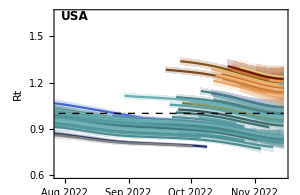
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

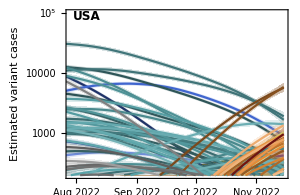
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

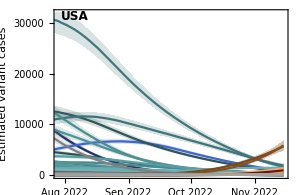
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,0.5}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

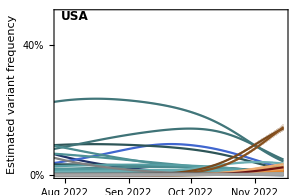
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{0.7,1.55},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

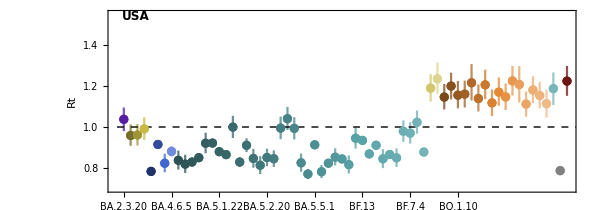

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.26},{0.7,1.55}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

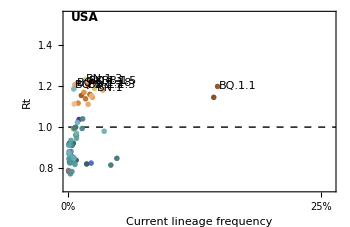
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
BN.1.3 | 1.23 | 1.16 - 1.31
BQ.1.1.5 | 1.22 | 1.15 - 1.3
XBB.1 | 1.22 | 1.15 - 1.3
BQ.1.1.18 | 1.22 | 1.13 - 1.31
BQ.1.1.7 | 1.21 | 1.12 - 1.3
BQ.1.1.3 | 1.21 | 1.14 - 1.28
BQ.1.1 | 1.2 | 1.13 - 1.26
BN.1 | 1.19 | 1.12 - 1.26

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png